## “Fibonacci” Cantor set

### Tests

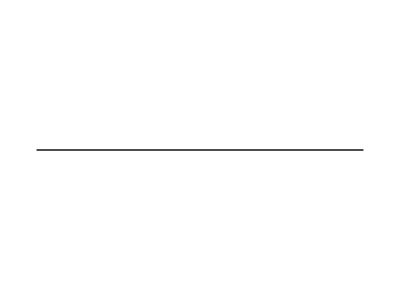

```mathematica
c0={{{0,0},{1,0}}};
Graphics[Line[c0]]
```

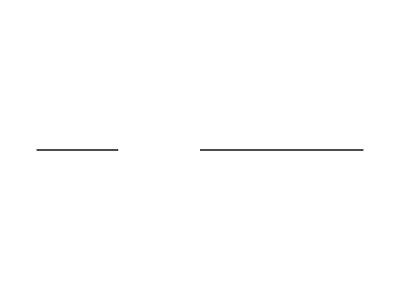

```mathematica
c1={{{0,0},{1/4,0}},{{1/2,0},{1,0}}};
Graphics[Line[c1]]
```

```mathematica
c1[[1]]
```

{{0,0},{1/4,0}}

```mathematica
EuclideanDistance[{1/4,0},{2/4,0}]
```

1/4

```mathematica
EuclideanDistance@@c1[[1]]
```

1/4

```mathematica
EuclideanDistance@@#&/@c1
```

{1/4,1/2}

```mathematica
(* prend en argument une "chaîne", ie un couple de points X, retourne les deux chaînes de l'étape suivante de construction de l'ensemble de Cantor *)
iter[X_]:=Module[{O,l},
O=X[[1]][[1]]; (* origine de la chaîne *)
l=EuclideanDistance@@X; (* longueur de la chaîne *)
{{{O,0},{O+l/4,0}},{{O+l/2,0},{O+l,0}}}
]
```

```mathematica
Flatten[iter/@c0,1]==c1
```

True

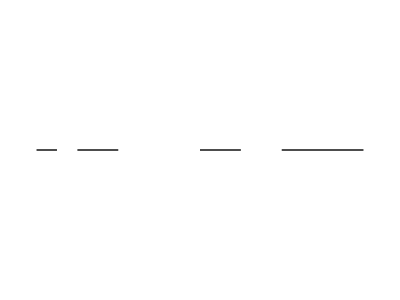

```mathematica
Graphics[Line[Flatten[iter/@c1,1]]]
```

### Dessin de l’ensemble

```mathematica
(* prend en argument un "segment", ie un couple de points X, retourne les deux segments de l'étape suivante de construction de l'ensemble de Cantor *)
iter[X_]:=Module[{O,l},
O=X[[1]][[1]]; (* origine du segment *)
l=EuclideanDistance@@X; (* longueur du segment *)
{{{O,0},{O+l/4,0}},{{O+l/2,0},{O+l,0}}}
]
c0={{{0,0},{10,0}}};
Manipulate[Graphics[Line[Nest[Flatten[iter/@#,1]&,c0,n]]],{n,0,5,1}]
```

```mathematica
dir=NotebookDirectory[];
```

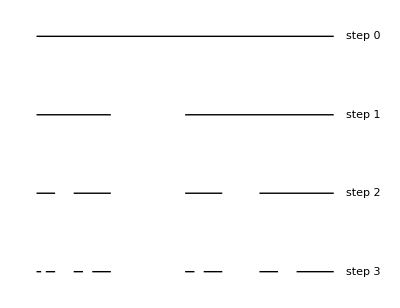

```mathematica
GraphicsColumn[Graphics[{Thick,Line[Nest[Flatten[iter/@#,1]&,c0,#]],Text["step "<>ToString@#,{11,0}]}]&/@Range[0,3]]
```

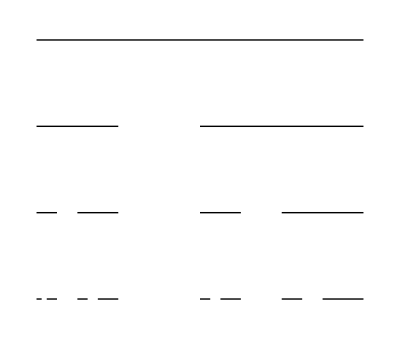

/home/nicolas/git/spectrum_quasicrystals/two_scales_cantor_set.pdf

```mathematica
g0=Graphics[{Thick,Line[Nest[Flatten[iter/@#,1]&,c0,0]]}];
g1=Graphics[{Thick,Line[Nest[Flatten[iter/@#,1]&,c0,1]]}];
g2=Graphics[{Thick,Line[Nest[Flatten[iter/@#,1]&,c0,2]]}];
g3=Graphics[{Thick,Line[Nest[Flatten[iter/@#,1]&,c0,3]]}];
GraphicsColumn[{g0,g1,g2,g3}]
Export[dir<>"two_scales_cantor_set.pdf",%]
```

### Calcul des dimensions fractales

À l’étape 1 (n=1 dans le dessin précédent), la fonction de partition est
Γ^(1)= (1/3)^q/(1/4)^τ + (2/3)^q/(1/2)^τ
à l’étape n,
Γ^(n) = (Γ^(1))^n
(ceci est vrai pour tout ensemble construit en enlevant récursivement des sous-segments d’un segment initial)
De sorte que τ(q) est donné par
Γ^(1)= (1/3)^q/(1/4)^(τ(q)) + (2/3)^q/(1/2)^(τ(q)) = 1 		(1)
On va résoudre numériquement cette équation !

```mathematica
l1=1/2;l2=1/4;
p1=2/3;p2=1/3;
Block[{q=0},
NSolve[p1^q l1^-τ+p2^q l2^-τ==1,τ,Reals]
]
Log[GoldenRatio]/Log[2]//N
```

{{τ→-0.694242}}

0.694242

```mathematica
listq=Table[q,{q,-60,60,1}];
listtau=Flatten[τ/.Function[q,NSolve[p1^q l1^-τ+p2^q l2^-τ==1,τ,Reals]]/@listq];
```

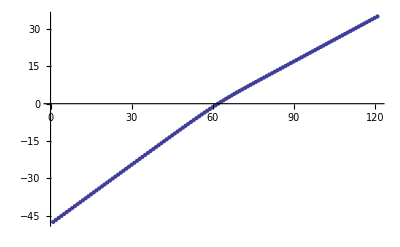

```mathematica
ListPlot[listtau]
```

```mathematica
listtau[[1]]
```

-0.694242

Comme α(q) = (dτ(q))/dq, en différentiant (1) on obtient une expression pour α :

```mathematica
α[q_,τ_]:=(Log[p1] p1^q l1^-τ+Log[p2] p2^q l2^-τ)/(Log[l1] p1^q l1^-τ+Log[l2] p2^q l2^-τ)
```

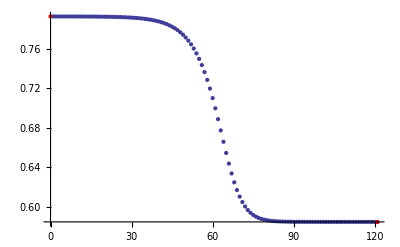

```mathematica
listα=MapThread[α,{listq,listtau}];
ListPlot[listα,Epilog->{PointSize[Large],Red,Point[{{2listq[[-1]]+1,Log[p1]/Log[l1]},{0,Log[p2]/Log[l2]}}]}]
```

On a simplement f(α) = q α - τ :

```mathematica
listf = listq*listα-listtau;
```

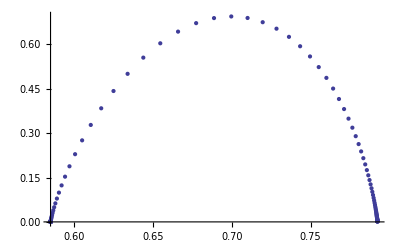

```mathematica
listfα=MapThread[{#1,#2}&,{listα,listf}];
ListPlot[listfα]
```

### Formule explicite pour les dimensions fractales

Dans ce cas particulier où l_1/l_2 = 2, on peut transformer l’équation implicite (1) en une équation polynomiale en posant τ(q) = log(x(q))/log(2) :
x^2 + 2^q x - 3^q = 0
La solution est donnée par :

```mathematica
x[q_]:=2^(q-1)(√(1+4*(3/4)^q)-1)
```

```mathematica
Clear[tau]
tau[q_]:=Log[x[q]]/Log[2]
```

```mathematica
tau[0]==Log[GoldenRatio^-1]/Log[2]//Simplify
```

True

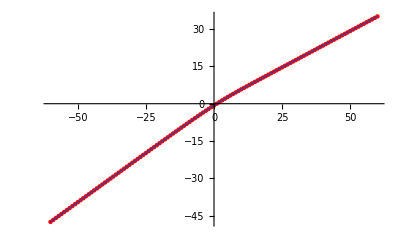

```mathematica
Plot[tau[q],{q,-60,60},Prolog->{Red,PointSize[.008],Point[MapThread[{#1,#2}&,{listq,listtau}]]}]
```

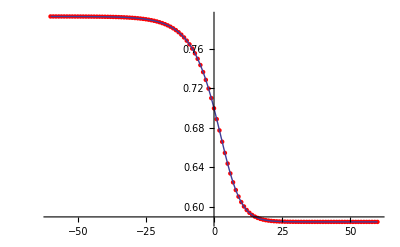

```mathematica
Plot[tau'[q],{q,-60,60},Prolog->{Red,PointSize[.008],Point[MapThread[{#1,#2}&,{listq,listα}]]}]
```

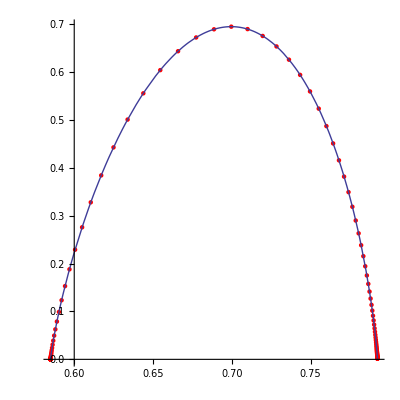

```mathematica
ParametricPlot[{tau'[q],q tau'[q] - tau[q]},{q,-60,60},Prolog->{Red,PointSize[.008],Point[listfα]},AspectRatio->1]
```

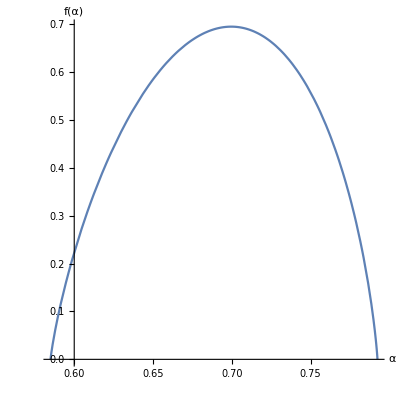

/home/nicolas/git/spectrum_quasicrystals/f_alpha_2_scales_cantor_set.pdf

```mathematica
ParametricPlot[{tau'[q],q tau'[q] - tau[q]},{q,-80,60},AspectRatio->1,PlotRange->All,AxesLabel->{α,f[α]}]
Export[dir<>"f_alpha_2_scales_cantor_set.pdf",%]
```